# Analytical Mechanics I

## Basic computational analysis for simple classical systems

Marion Book

By: Omar H. Mashaal

## Part I: Linear Oscillations

## Simple Harmonic Motion

### Equation of motion

```mathematica
Clear["Global`*"]
DSolve[x''[t]+w^2 x[t]==0,x[t],t]
```

{{x[t]→C[1] Cos[t w]+C[2] Sin[t w]}}

#### 1D Solution

```mathematica
x[t_,A_,m_,k_,xPh_]:= A* Cos[(k/m)^(1/2)*t-xPh]
Manipulate[Plot[{x[t,A,m,k,xPh]},
		{t,0,(2Pi/(k/m)^(1/2))},
		(*PLotting options*)
		PlotLabel->"1D Oscillation",
		AxesLabel->{"t","x(t)"},
		GridLines->Automatic],{m,1,100},{k,1,10},{A,1,10},{xPh,0,Pi}]
```

#### 2D

```mathematica
x[t_,A_,wx_,xPh_] := A Cos[wx t-xPh]
y[t_,B_,wy_,yPh_] := B Cos[wy t-yPh]
Manipulate[ParametricPlot[{x[t,A,wx,xPh],y[t,B,wy,yPh]},
		{t,0,time},
		(*PLotting options*)
		AxesLabel->{"x(t)","y(t)"},
		PlotLabel->"2D Oscillation",
		AxesOrigin->Automatic,
		PlotLegends -> {"Ph diff:"+(xPh-yPh), "Omeg ratio:" (wy/wx)}],
                    {time,100,1000},{wy,2,10},{wx,1,10},
                    {xPh,0,Pi},{yPh,0.5 Pi,Pi},{A,1,10},{B,1,10}]
```

#### 3D

```mathematica
x[t_,A_,wx_,xPh_] := A Cos[wx t-xPh]
y[t_,B_,wy_,yPh_] := B Cos[wy t-yPh]
z[t_,C_,wz_,zPh_] := C Cos[wz t-zPh]
Manipulate[ParametricPlot3D[{x[t,A,wx,xPh],y[t,B,wy,yPh],z[t,C,wz,zPh]},
		{t,0,time},
		(*PLotting options*)
		AxesLabel->{"z(t)","y(t)","x(t)"},
		PlotLabel->"3D Ocillation",
		AxesOrigin->Automatic],{time,100,1000},
		{wx,1,10},{wy,1,10},{wz,1,10},
		{xPh,0,Pi},{yPh,0,Pi},{zPh,0,Pi},
		{A,1,10},{B,1,10},{C,1,10}]
```

### Phase space

```mathematica
Clear["Global`*"]
Eliminate[{x==A*Sin[w*t],Vx==-A*w*Cos[w*t]},t]
```

Eliminate::ifun: Inverse functions are being used by Eliminate, so some solutions may not be found; use Reduce for complete solution information.

Vx^2==w^2 (A^2-x^2)&&Vx^2/w^2==A^2-x^2&&-Vx^2/w==w (-A^2+x^2)&&x^2/A^2==1-Vx^2/(A^2 w^2)&&x^2/A==A (1-Vx^2/(A^2 w^2))

```mathematica
Clear["Global`*"]
x[t_,A_,m_,k_]:= A* Sin[(k/m)^(1/2)*t]
Vx[t_,A_,m_,k_] := D[x[t,A,m,k],t]
Manipulate[ParametricPlot[{x[t,A,m,k],
					Vx[t0,A,m,k]/. t0->t},
		{t,0,time},
		(*PLotting options*)
		AxesLabel->{"x","v"},
		PlotLabel->"Phase Space",
		AxesOrigin->Automatic,
		GridLines->Automatic,
		PlotLegends -> {"A=1, w=1"}],{time,1,2Pi/(k/m)^0.5},{k,1,10},{m,1,10},{A,1,10}]
```

### Mechanical Energy

#### As a function of time

```mathematica
Clear["Global`*"]
x[t_,A_,m_,k_]:= A* Cos[(k/m)^(1/2)*t]
Vx[t_,A_,m_,k_] := D[A* Cos[(k/m)^(1/2)*t],t]
KE_tAVG =(Integrate[0.5*m*Vx[t,A,m,k]^2,{t,0,2Pi/(k/m)^(1/2)}])/(2Pi/(k/m)^(1/2)) //FullSimplify
PE_tAVG =(Integrate[0.5*k*x[t,A,m,k]^2,{t,0,2Pi/(k/m)^(1/2)}])/(2Pi/(k/m)^(1/2)) // FullSimplify
```

0.25 A^2 k

0.25 A^2 k

```mathematica
Manipulate[Plot[{0.5*m*Vx[t0,A,m,k]^2/.t0->t,
		0.5*k*x[t,A,m,k]^2,
		0.5*k*x[t,A,m,k]^2+0.5*m*Vx[t0,A,m,k]^2/.t0->t},
		{t,0,(2Pi/(k/m)^(1/2))},
		(*PLotting options*)
		AxesLabel->{"t","E(t)"},
		PlotLabel->"Energy over one period",
		GridLines->Automatic,
		PlotLegends -> {"KE(t)","PE(t)","KE+PE"}],{m,1,100},{k,1,10},{A,1,10}]
```

#### As a function of space

```mathematica
Clear["Global`*"]
x[t_,A_,m_,k_]:= A* Cos[(k/m)^(1/2)*t]
Vx[t_,A_,m_,k_] := D[A* Cos[(k/m)^(1/2)*t],t]
KE_sAVG=(Integrate[0.5m ((k/m)^0.5)^2(A^2-x^2),{x,0,A}])/A //FullSimplify
PE_sAVG=(Integrate[0.5k x^2,{x,0,A}])/A//FullSimplify
```

0.333333 A^2 k

0.166667 A^2 k

```mathematica
Manipulate[Plot[{0.5m ((k/m)^0.5)^2 (A^2-x^2),
		0.5k x^2, 0.5m (A(k/m)^0.5)^2(A^2-x^2) + 0.5k x^2},
		{x,-A,A},
		(*PLotting options*)
		AxesLabel->{"x","E(x)"},
		PlotLabel->"Energy over one period",
		GridLines->Automatic,
		PlotLegends -> {"KE(t)","PE(t)","KE+PE"}],{m,1,100},{k,1,10},{A,1,10}]
```

## Damped Oscillation

### Equation of motion

```mathematica
Clear["Global`*"]
DSolve[x''[t]+2B*x'[t]+w0^2*x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(t (-B-√(B^2-w0^2))) C[1]+ⅇ^(t (-B+√(B^2-w0^2))) C[2]}}

### Under-damped case (w > B)

#### Solution

```mathematica
Clear["Global`*"]
x[t_,A_,B_,w0_,xPh_] := A ⅇ^(-B t) Cos[(w0^2-B^2)^(1/2)t+xPh]
decay[t_,A_,B_]:= A ⅇ^(-B t) 
Manipulate[Plot[{x[t,A,B,w0,xPh],decay[t,A,B]},{t,0,time},
(*PLotting options*)
		AxesLabel->{"t","x(t)"},
		GridLines->Automatic,
		PlotLabel->"Under-damped",
		PlotLegends -> {"Oscillation","Decaying rate"}],
{time,1,10},{B,1,9},{A,1,10},{w0,10,100},{xPh,0,Pi}]
```

#### Mechanical Energy

```mathematica
Clear["Global`*"]
x[t_,A_,B_,w0_,xPh_] :=A ⅇ^(-B t) Cos[(w0^2-B^2)^(1/2)t+xPh]
Vx[t_,A_,B_,w0_,xPh_] :=D[ A ⅇ^(-B t) Cos[(w0^2-B^2)^(1/2)t+xPh],t]
Manipulate[Plot[{0.5 m w0^2 x[t,A,B,w0,xPh]^2,
			    0.5 m  Vx[t0,A,B,w0,xPh]^2/.t0->t,
			    0.5 m w0^2 x[t,A,B,w0,xPh]^2+0.5 m Vx[t0,A,B,w0,xPh]^2/.t0->t},
			      {t,0,time},
		(*PLotting options*)
		AxesLabel->{"t","E(t)"},
		GridLines->Automatic,
		PlotLegends -> {"PE","KE","Total"}],
		{time,1,10},{B,1,9},{A,1,10},{w0,10,100},{xPh,0,Pi},{m,1,10}]
```

#### Rate of change of energy

```mathematica
Clear["Global`*"]
dEdt[t_,A_,B_,w0_,xPh_,m_]:=D[ 0.5 m w0^2 (A ⅇ^(-B t) Cos[(w0^2-B^2)^(1/2)t+xPh])^2+0.5 m (D[ A ⅇ^(-B t) Cos[(w0^2-B^2)^(1/2)t+xPh],t])^2,t]
Manipulate[Plot[{dEdt[t0,A,B,w0,xPh,m]/. t0->t},
			{t,0,time},
		(*PLotting options*)
		AxesLabel->{"t","dE/dt"},
		PlotLabel->"Rate of change of energy",
		GridLines->Automatic,
		PlotLegends -> {"KE","PE","E total"}],
		{time,1,2 Pi /(w0^2-B^2)^(1/2)},{B,1,9},{A,1,10},{w0,10,100},{xPh,0,Pi},{m,1,10}]
```

#### Phase space

```mathematica
Clear["Global`*"]
x[t_,A_,B_,w0_,xPh_] :=A ⅇ^(-B t) Cos[(w0^2-B^2)^(1/2)t+xPh]
Vx[t_,A_,B_,w0_,xPh_] :=D[ A ⅇ^(-B t) Cos[(w0^2-B^2)^(1/2)t+xPh],t]
Manipulate[ParametricPlot[{x[t,A,B,w0,xPh]*10,Vx[t0,A,B,w0,xPh]/.t0->t},
		{t,0,time},
		(*PLotting options*)
		AxesLabel->{"x(t)","Vx(t)"},
		PlotLabel->"Phase Diagram",
		AxesOrigin->Automatic,
		GridLines->Automatic],{time,1,10},{w0,10,100},{xPh,0,Pi},{A,1,10},{B,1,9}]
```

### Critically-damped case (w = B)

#### Solution

```mathematica
Clear["Global`*"]
x[t_,A_,B_,C_] := (A +C t)ⅇ^(-B t) 
Manipulate[Plot[{x[t,A,B,C],(A +C t)},{t,0,time},
(*PLotting options*)
		AxesLabel->{"t","x(t)"},
		PlotLabel->"Critically-damped",
		GridLines->Automatic,
		PlotLegends -> {"Decaying","Line amplitiude"}],{time,1,10},{B,1,10},{A,1,10},{C,0,Pi}]
```

### Over-damped case (w < B)

#### Solution

```mathematica
Clear["Global`*"]
x[t_,A1_,A2_,B_,w0_] := ⅇ^(-B t)(A1 ⅇ^((B^2-w0^2)^0.5 t)+A2 ⅇ^(-(B^2-w0^2)^0.5 t)) 
Manipulate[Plot[{x[t,A1,A2,B,w0]},{t,0,time},
(*PLotting options*)
		AxesLabel->{"t","x(t)"},
		PlotLabel->"Over-damped",
		GridLines->Automatic],{time,1,2Pi/w0},
{B,10,100},{A1,1,10},{A2,1,10},{w0,1,9}]
```

## Driven Oscillation

### Equation of motion

#### Solution

```mathematica
Clear["Global`*"]
DSolve[x''[t]+2B*x'[t]+w0^2*x[t]==A Cos[wd t],x[t],t]//FullSimplify
DSolve[x''[t]+2B*x'[t]+w0^2*(x[t]-x0)==A Cos[wd t],x[t],t]//FullSimplify
```

{{x[t]→ⅇ^(-t (B+√(B^2-w0^2))) (C[1]+ⅇ^(2 t √(B^2-w0^2)) C[2])+(A (w0-wd) (w0+wd) Cos[t wd]+2 A B wd Sin[t wd])/(w0^4-2 (-2 B^2+w0^2) wd^2+wd^4)}}

{{x[t]→x0+ⅇ^(-t (B+√(B^2-w0^2))) (C[1]+ⅇ^(2 t √(B^2-w0^2)) C[2])+(A (w0-wd) (w0+wd) Cos[t wd]+2 A B wd Sin[t wd])/(w0^4-2 (-2 B^2+w0^2) wd^2+wd^4)}}

```mathematica
Clear["Global`*"]
dforce[t_,Af_,w_] := Af Cos[w t]
xc[t_,Ac_,w_,w0_,B_] := Ac ⅇ^(-B t) Cos[(w0^2-B^2)^(1/2)t]
xp[t_,Af_,w_,w0_,B_,ph_] := (Af/((w0^2-w^2)^2 + 4 B^2 w^2 )^0.5) Cos[w t-ph]
x[t_,Ac_,Af_,w_,w0_,B_,ph_] := xc[t,Af,w,w0,B]+xp[t,Af,w,w0,B,ph] 
Manipulate[Plot[{xc[t,Ac,w,w0,B], xp[t,Af,w,w0,B,ph],x[t,Ac,Af,w,w0,B,ph]},{t,0,time},
(*PLotting options*)
		AxesLabel->{"t","x(t)"},
		GridLines->Automatic,
		PlotLegends -> {"Complementray Sol","Particular Sol", "Final Sol"}],
{time,10,100},{B,0.15,1},{w,2,10},{w0,1,10},{ph,0,Pi},{Af,2,10},{Ac,1,10},{c2,1,10},{c1,2,10}]
```

#### Phase between driving force and particular solution

```mathematica
Clear["Global`*"]
B=0.1; Af = 1; ph=0;
dforce[t_,Af_,w_] := Af Cos[w t]
xp[t_,Af_,w_,w0_,B_,ph_] := (Af/((w0^2-w^2)^2 + 4 B^2 w^2 )^0.5) Cos[w t-ph]
Manipulate[Plot[{ xp[t,Af,w,w0,B,ph],dforce[t,Af,w]},{t,0,100},
(*PLotting options*)
		AxesLabel->{"t","x(t)"},
		GridLines->Automatic,
		PlotLabel->ArcTan[2B w/w0^2-w^2],
		PlotLegends -> {"force Sol","Particular Sol"}],
		{w,0,2},{w0,0.1,2}]
```

### Resonance Phenomenon

#### Solving for Resonance Frequency

```mathematica
Clear["Global`*"]
Amp[Af_,w0_,w_,B_]:=Af/((w0^2-w^2)^2+ 4 B^2 w^2)^0.5
Solve[D[Amp[Af,w0,w,B],w] ==0,w]
```

{{w→0.},{w→-1. √(-2. B^2+1. w0^2)},{w→√(-2. B^2+1. w0^2)}}

#### Quality Factor

```mathematica
Clear["Global`*"]
Af=1; w0=1;
Amp[Af_,w0_,w_,B_]:=Af/((w0^2-w^2)^2+ 4 B^2 w^2)^0.5
Manipulate[Plot[{Amp[Af,w0,w,B],Amp[Af,1,w,0.1],Amp[Af,1,w,0.2],Amp[Af,1,w,0.3]},{w,0.1,wmax},
(*PLotting options*)
		AxesLabel->{"w","D"},
		GridLines->Automatic,
		PlotLabel->"Measure of system's response to the applied power",
PlotLegends -> {"Aribitrary B","B=0.1","B=0.2","B=0.3"}],
{B,0.1,1},{wmax,2,10}]
```

### Fourier series

#### Step function

```mathematica
Clear["Global`*"]
(*Define the function and half of the period*)
w=1; p=w/Pi;
f[t_]:=Piecewise[{{-1,-p<t<=0},{1,0<t<=p}}]
(*Coefficients*)
a0=(Integrate[f[t],{t,-p,p}])/2p
an=(Integrate[f[t]*Cos[t(n Pi)/p],{t,-p,p}])/p
bn=(Integrate[f[t]* Sin[t(n Pi)/p],{t,-p,p}])/p
(*Fourier Series*)
fourier[t_,N_]:=a0+ ∑_(n=1)^N an*Cos[t(n Pi)/p] + ∑_(n=1)^N bn*Sin[t(n Pi)/p]
Manipulate[Plot[{f[t],fourier[t,N]},{t,-p,p}],{N,1,100}]
```

0

0

-(2 (-1+Cos[n π]))/(n π)

#### Sawtooth function

```mathematica
Clear["Global`*"]
(*Define the function and half of the period*)
tau=2 Pi/w; w=1; p= tau/2;
f[t_]:=Piecewise[{{t/tau,-p<t<=p}},0]
(*Coefficients*)
a0=(Integrate[f[t],{t,-p,p}])/2p
an=(Integrate[f[t]*Cos[t(n Pi)/p],{t,-p,p}])/p
bn=(Integrate[f[t]* Sin[t(n Pi)/p],{t,-p,p}])/p
(*Fourier Series*)
fourier[t_,N_]:=a0+ ∑_(n=1)^N an*Cos[t(n Pi)/p] + ∑_(n=1)^N bn*Sin[t(n Pi)/p]
Manipulate[Plot[{f[t],fourier[t,N]},{t,-p,p}],{N,1,100}]
```

0

0

(-n π Cos[n π]+Sin[n π])/(n^2 π^2)

### Response of the system for different forces

#### Heaviside force function

```mathematica
(*Equation of motion is simply*)
DSolve[x''[t]+2B*x'[t]+w0^2*x[t]==c,x[t],t]// FullSimplify
```

{{x[t]→c/w0^2+ⅇ^(-t (B+√(B^2-w0^2))) (C[1]+ⅇ^(2 t √(B^2-w0^2)) C[2])}}

```mathematica
(*This is the solution of underdamped + constant c/w so we can write it as*)
x[t_,A1_,A2_,B_,w0_,c_] :=c/w0^2+ (ⅇ^(-B t))[A1 Cos[(w0^2-B^2)^(1/2)t]+A2 Sin[(w0^2-B^2)^(1/2)t]]
```

```mathematica
(*Initial Conditions x(t=0) = 0 and Vx(t=0) = 0 Error!!*)
```

```mathematica
Solve[x[0,A1,A2,B,w0,c]==0,A1]
Solve[x'[0,A1,A2,B,w0,c]==0 ,A2]
```

```mathematica
Clear["Global`*"]
(*Define the function*)
B1=0.2; B2=0; w0=1;
heaviside[t_,c_,t0_]:=Piecewise[{{0,t<t0},{c,t>t0}},0]
x[t_,t0_,B_,w0_,c_] :=c/w0^2+ⅇ^(-B t)(-(c/w0) Cos[(w0^2-B^2)^(1/2)(t-t0)]-(c B / w0^2(w0^2-B^2)^(1/2) ) Sin[(w0^2-B^2)^(1/2)(t-t0)])
Manipulate[Plot[{heaviside[t,c,t0],x[t,t0,B1,w0,c],x[t,t0,B2,w0,c]},{t,0,10}],{c,0.1,1},{t0,0,10}]
```

#### Impulse force function

```mathematica
Clear["Global`*"]
(*Define the function*)
(*Impulse = H(t0)-H(t1)*)
 w0=1; B=0.2 w0; t0=0; tau=(2 Pi/(w0^2-B^2)^(1/2)); w1=(w0^2-B^2)^(1/2);
heaviside[t_,c_,t0_]:=Piecewise[{{0,t<t0},{c,t>t0}},0]
impulse[t_,t0_,tau_,c_]:=heaviside[t,c,t0]-heaviside[t,c,t0+tau]
x[t_,t0_,tau_,B_,w0_,c_] :=(c ⅇ^(-B (t-t0)))/w0^2(ⅇ^(B tau)( Cos[w1(t-t0)]Cos[w1 tau]+Sin[w1(t-t0)]Sin[w1 tau])-
Cos[w1(t-t0)]   + ((B ⅇ^(B tau))/w1)(Sin[w1(t-t0)]Cos[w1 tau]-Cos[w1(t-t0)]Sin[w1 tau])-
(B/w1)Sin[w1(t-t0)])
Manipulate[Plot[{impulse[t,t0,tau,c],x[t,t0,tau,B,w0,c]},{t,t0,10}],{c,1,2},{t0,0,40}]
```

## II: Non-linear Oscillations

## First Correction

### Symmetric Correction

#### Potential

```mathematica
Clear["Global`*"]
k=1; 
u[x_,c_]:= 1/2 k x^2 - c x^4
Manipulate[Plot[{u[x,0],u[x,c]},{x,-1,1},
		(*PLotting options*)
		PlotLabel->"Potentail Energy",
		AxesLabel->{"x","PE(x)"},
		PlotLegends -> {"Linear", "First correction"}],{c,-1,1}]
```

#### Force

```mathematica
f[x_,c_]:=D[u[x,c],x]
Manipulate[Plot[{f[x0,0]/. x0->x,f[x1,c]/. x1->x},{x,-1,1},
		(*PLotting options*)
		PlotLabel->"Force",
		AxesLabel->{"x","F(x)"},
		PlotLegends -> {"Linear", "First correction"}],{c,-1,1}]
```

### Asymmetric Correction

#### Potential

```mathematica
Clear["Global`*"]
k=1; 
u[x_,c_]:= 1/2 k x^2 - c x^3
Manipulate[Plot[{u[x,0],u[x,c]},{x,-1,1},
		(*PLotting options*)
		PlotLabel->"Potentail Energy",
		AxesLabel->{"x","PE(x)"},
		PlotLegends -> {"Linear", "First correction"}],{c,-1,1}]
```

#### Force

```mathematica
f[x_,c_]:=D[u[x,c],x]
Manipulate[Plot[{f[x0,0]/. x0->x,f[x1,c]/. x1->x},{x,-1,1},
		(*PLotting options*)
		PlotLabel->"Force",
		AxesLabel->{"x","F(x)"},
		PlotLegends -> {"Linear", "First correction"}],{c,-1,1}]
```

## Interesting phenomenons

### Hysteresis k(x)

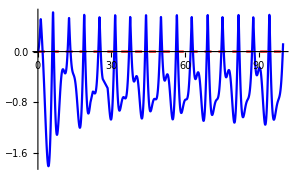
Row[-Graphics-,]

```mathematica
Clear["Global`*"]
(* Numericaly solve for k(x) *)
With[{k1=1,k2=80,m=1,w=1, B=0.1,a=0.5},s1 = NDSolve[{y[t]==x'[t],y'[t]+B*y[t]+If[x[t]<a,k1,k2-a(k2-k1)]/m x[t]==Cos[w t],x[0]==0.0, y[0]==0},{x,y},{t,400}]];
(*Visualize*)
tmax=20;
Row[
Plot[{0,x[t] /. s1},{t,0,100},PlotStyle-> {{Red,Dashed},Blue}, ImageSize->300]
(*Animation*),
ListAnimate@Table[
Plot[{0,x[t] /. s1},{t,0,tmax},PlotRange->{{0,tmax},{-2,2}}],{tmax,1,tmax,0.1}
]
]
```

```mathematica
A[x_]:=Piecewise[{{F/(√((k1-m w^2)^2 + (2 B w)^2)),x<a},{F/(√((k2-m w^2)^2 + (2 B w)^2)),x>a}}];
ph[x_]:=Piecewise[{{(B w)/(k1-m w^2),x<a},{(B w)/(k2-m w^2),x>a}}];

sol[t_,x_]:=Piecewise[{{A[x] * Cos[w t-ph[x]],x<a},{a(k2-k1)+A[x] * Cos[w t-ph[x]],x>a}}];
Manipulate[Plot[{a,sol[t,x]},{t,0,4}],{x,0,10}]
```

### Van Pol Equation ẋ(x)

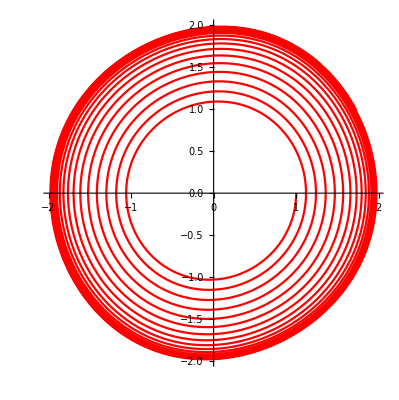

```mathematica
μ= 0.05; a = 1; ω=1; tmax = 100;
(* Initial conditions: x[0]== 1.50 and speed = 0 *)
s1=NDSolve[{x'[t]==y[t],y'[t]+μ (x[t]^2-a^2)y[t]+ ω^2 x[t]==0,x[0]== 1,y[0]==0},{x,y},{t,tmax}];
p1 =ParametricPlot[Evaluate[{x[t],y[t]}/.s1],{t,0,tmax},PlotStyle-> Red,PlotRange->All,LabelStyle->18];
Show[p1]
```

### Driven Non-linear Pendulum

#### Description

The torque around the pivot point 
-Graphics-

dividing by  I = m l^2
-Graphics-

We cast it into the dimensionless form by dividing by ω_0^2=g/l

-Graphics-

-Graphics-    -Graphics-

#### Solving the equation (Chaos at f0 = 0.6)

```mathematica
c= 0.05; w=0.7; tmax = 700; f0 = 0.4(* f0 -> driving strength *);
s1=NDSolve[{x'[t]==y[t],y'[t]+c y[t]+ Sin[x[t]]-f0 Cos[w t]==0.0,x[0]== 1,y[0]==0},{x,y},{t,tmax}];
Row[
Manipulate[Plot[Evaluate[y[t]/.s1],{t,0,time},AxesLabel->{"t'","y(t')"},ImageSize->Medium],{time,100,tmax}],
(*Phase diagram*)
Manipulate[ParametricPlot[Evaluate[{y[t],x[t]}/. s1],{t,0,time}, ImageSize->Small],{time,100,tmax}]
]
```

Row[,]

#### Poincare sections

### Bifurcation diagram (Logistic map)

#### Diagram

```mathematica
αStep = 0.001; αStart =2.9; αEnd =3.8;
α = Range[αStart,αEnd,αStep];
αxList = 0α;

ns = 100 (* ns = number of iteration. Larger values needed for stablitiy *)
nb=200 (* nb = maximum number of bifurcations shown in the plot *)

x =Table[0,{i, Length[α]},{j,nb}];
xn = Table[0,{i, ns}]; (* List of x values *)
xn[[1]]=0.5; (* Initial value of x *)

Do[ 
Do[xn[[i]]=α[[nα]]xn[[i-1]](1-xn[[i-1]])
,{i,2,ns}];
x[[nα]] =xn[[-nb;;-1]],{nα,Length[α]}];

αxList = Table[{α[[nα]],x[[nα,i]]},{i, nb},{nα,Length[α]}];
ListPlot[αxList, AxesLabel->{"α","x_n"},LabelStyle->18]
```

#### Feigenbaum’s number

### Chaos identification; Lyapunov Exponent

#### Sensitivity to initial condition

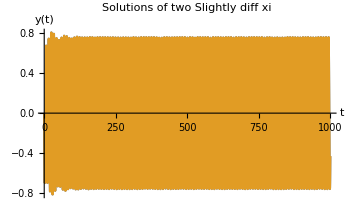
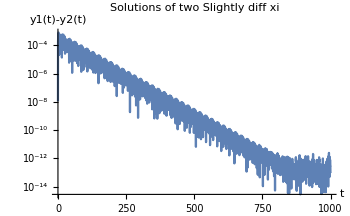
Row[-Graphics-,-Graphics-]

{-13.3579}

```mathematica
Clear["Global`*"]
c= 0.05; w=0.7;f0 = 0.4;tmax=1000;diff = 0.001; init = 1.000;
(* For X_initial = 1 *)
s1=NDSolve[{x'[t]==y[t],y'[t]+c y[t]+ Sin[x[t]]-f0 Cos[w t]==0.0,x[0]== init,y[0]==0},{x,y},{t,tmax}];
s2=NDSolve[{xx'[t]==yy[t],yy'[t]+c yy[t]+ Sin[xx[t]]-f0 Cos[w t]==0.0,xx[0]== init+diff,yy[0]==0},{xx,yy},{t,tmax}];
Row[
Plot[{Evaluate[y[t]/. s1],Evaluate[yy[t]/. s2]},{t,0,tmax}, ImageSize->350,PlotLabel->"Solutions of two Slightly diff xi", AxesLabel->{"t","y(t)"}],
LogPlot[{Abs[Evaluate[y[t]/. s1]-Evaluate[yy[t]/. s2]]},{t,0,tmax}, ImageSize->350,PlotLabel->"Solutions of two Slightly diff xi", AxesLabel->{"t","y1(t)-y2(t)"}]
]
(* Calaculating exponent *)
λ=1/tmax∑_(t=1)^(tmax-1) Log[Abs[Evaluate[y[t]/. s1]-Evaluate[yy[t]/. s2]]/diff]
```

## III: Gravitation

## Potential and Gravitational Field

### Point Mass

#### Potential

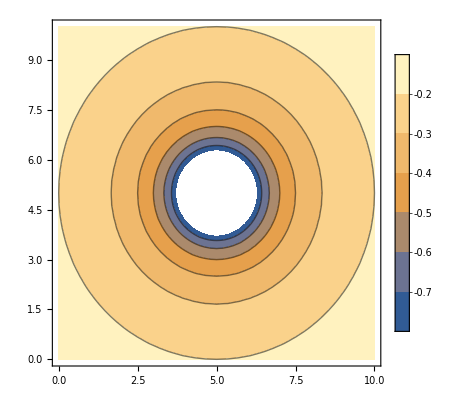
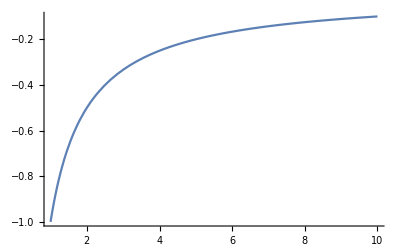
Row[-Graphics-,-Graphics-]

```mathematica
Clear["Global`*"]
G=1;
 x1 = 5;y1=5; m1=1;
phi1[x_,y_]:=(- G m1)/(((x-x1)^2+(y-y1)^2)^0.5);
phip[r_]:=(- G m1)/r;
Row[
ContourPlot[{phi1[x,y]},{x,0,10},{y,0,10}, PlotLegends->Automatic,ImageSize->{Automatic,250}],
Plot[phip[r],{r,1,10},ImageSize->{Automatic,250}]
]
```

```mathematica
Clear["Global`*"]
G=1;
m1=1; 
m2=2;x2 = 8;y2=4;
m3=1.5;x3 = 4.5;y3=8;
phi1[x_,y_,x1_,y1_]:=(- G m1)/(((x-x1)^2+(y-y1)^2)^0.5);
phi2[x_,y_]:=(- G m2)/(((x-x2)^2+(y-y2)^2)^0.5);
phi3[x_,y_]:=(- G m3)/(((x-x3)^2+(y-y3)^2)^0.5);
Manipulate[ContourPlot[{phi1[x,y,x1,y1]+phi2[x,y]+phi3[x,y]},{x,0,10},{y,0,10}, PlotLegends->Automatic],{x1,1,10},{y1,1,10}]
```

#### Gravitational Field

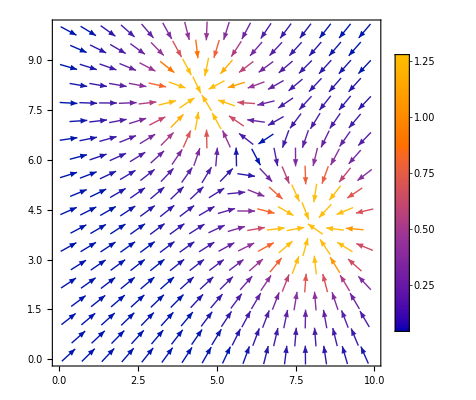

```mathematica
fx=-D[phi2[x,y]+phi3[x,y],x];
fy=-D[phi2[x,y]+phi3[x,y],y];
VectorPlot[{fx,fy},{x,0,10},{y,0,10}, PlotLegends->Automatic]
```

### Uniform Rod

#### Potential

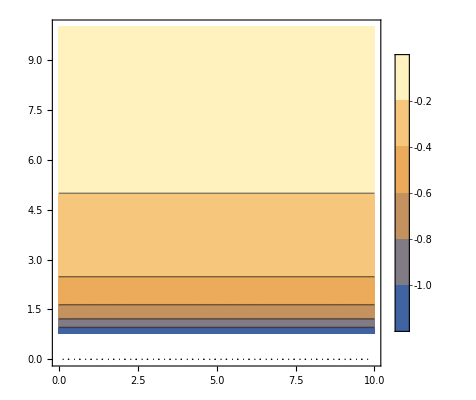
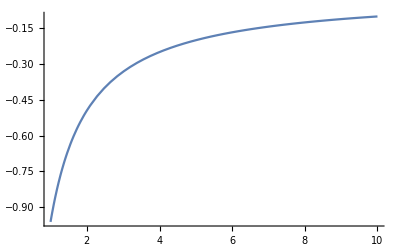
Row[-Graphics-,-Graphics-]

```mathematica
Clear["Global`*"]
G=1;
 x1 =5; y1=5; m1=1; l=1;
phi[y_]:=(- G m1)/l Log[(√(l^2+4 y^2)+l)/(√(l^2+4 y^2)-l)];
Row[
ContourPlot[phi[y],{x,0,10},{y,0,10}, ImageSize->{Automatic,250},PlotLegends->Automatic],
Plot[phi[y],{y,1,10},ImageSize->{Automatic,250}]
]
```

#### Gravitation Field

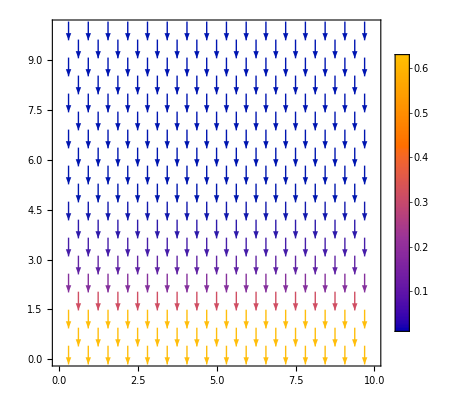

```mathematica
fx=0;
fy=-D[phi[y],y];
VectorPlot[{fx,fy},{x,0,10},{y,0,10}, PlotLegends->Automatic]
```

```mathematica
Clear["Global`*"]
DSolve[x''[t]+u(x[t]^2-1) * x'[t]+x[t]==0,x[t],t]
```

DSolve[x[t]+u (-1+x[t]^2) x'[t]+x''[t]==0,x[t],t]

## Tidal effect

### Moon effect

## V: Calculus of Variations

## Extremum of a functional

### Euler Equation

```mathematica
Clear["Global`*"]
xi=0;xf=2 Pi;
ym[x_] := 1x;
n[x_] := Sin[x/2];
yv[x_,a_] := ym[x]+a n[x];
ds[x_,a_]:=√(1+D[yv[x,a],x]^2);
ds[x,a]
J[a] :=Integrate[ds[x,a],x];
J[a]
Row[
Manipulate[Plot[{ym[x],yv[x,a]},{x,xi,xf},
AxesLabel->{"x","y(x)"},
GridLines->Automatic,
ImageSize->200,
PlotLegends -> {"Minimum Path","Varied path" }],{a,-2,2}],
Plot[J[a],{a,-2,2},
AxesLabel->{"a","J(a)"},
GridLines->Automatic,
ImageSize->200]
]
```

√(1+(1+1/2 a Cos[x/2])^2)

1/(√(-((-2+2 ⅈ)+a)/((2-2 ⅈ)+a)) √(16+a^2+8 a Cos[x/2]+a^2 Cos[x]))√2 Cos[x/4]^4 ((8 ⅈ+4 a-ⅈ a^2) EllipticE[ⅈ ArcSinh[√(-((-2+2 ⅈ)+a)/((2-2 ⅈ)+a)) Tan[x/4]],(-8-4 ⅈ a+a^2)/(-8+4 ⅈ a+a^2)] Sec[x/4]^2 √((((2-2 ⅈ)+a Cos[x/2]) Sec[x/4]^2)/((2-2 ⅈ)+a)) √((((2+2 ⅈ)+a Cos[x/2]) Sec[x/4]^2)/((2+2 ⅈ)+a))-(4-4 ⅈ) ((-2+2 ⅈ)+a) EllipticF[ⅈ ArcSinh[√(-((-2+2 ⅈ)+a)/((2-2 ⅈ)+a)) Tan[x/4]],(-8-4 ⅈ a+a^2)/(-8+4 ⅈ a+a^2)] Sec[x/4]^2 √((((2-2 ⅈ)+a Cos[x/2]) Sec[x/4]^2)/((2-2 ⅈ)+a)) √((((2+2 ⅈ)+a Cos[x/2]) Sec[x/4]^2)/((2+2 ⅈ)+a))-8 ⅈ a EllipticPi[-((2-2 ⅈ)+a)/((-2+2 ⅈ)+a),ⅈ ArcSinh[√(-((-2+2 ⅈ)+a)/((2-2 ⅈ)+a)) Tan[x/4]],(-8-4 ⅈ a+a^2)/(-8+4 ⅈ a+a^2)] Sec[x/4]^2 √((((2-2 ⅈ)+a Cos[x/2]) Sec[x/4]^2)/((2-2 ⅈ)+a)) √((((2+2 ⅈ)+a Cos[x/2]) Sec[x/4]^2)/((2+2 ⅈ)+a))+8 √(-((-2+2 ⅈ)+a)/((2-2 ⅈ)+a)) Tan[x/4]+4 a √(-((-2+2 ⅈ)+a)/((2-2 ⅈ)+a)) Tan[x/4]+a^2 √(-((-2+2 ⅈ)+a)/((2-2 ⅈ)+a)) Tan[x/4]+16 √(-((-2+2 ⅈ)+a)/((2-2 ⅈ)+a)) Tan[x/4]^3-2 a^2 √(-((-2+2 ⅈ)+a)/((2-2 ⅈ)+a)) Tan[x/4]^3+8 √(-((-2+2 ⅈ)+a)/((2-2 ⅈ)+a)) Tan[x/4]^5-4 a √(-((-2+2 ⅈ)+a)/((2-2 ⅈ)+a)) Tan[x/4]^5+a^2 √(-((-2+2 ⅈ)+a)/((2-2 ⅈ)+a)) Tan[x/4]^5)

Row[,-Graphics-]